# Versuch 31

```mathematica
ClearAll["Global`*"]
```

## Plot Settings

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

```mathematica
ungewichteterReg[xdata_,ydata_]:=Module[{sx2=Total[xdata^2],sy=Total[ydata],sx=Total[xdata],sxy=Sum[xdata[[i]]ydata[[i]],{i,1,Length[xdata]}], n=Length[xdata],Δ,a,b,σ},Δ=(n sx2-sx^2);a=1/Δ(sx2 sy-sx sxy); b=1/Δ(n sxy-sx sy);σ=Sqrt[1/(n-2) Sum[(ydata[[i]]-a - b xdata[[i]])^2,{i,1,n}]];{a,b,σ Sqrt[sx2/Δ], σ Sqrt[n/Δ]}]
```

## Import Data

```mathematica
rawData=Import[NotebookDirectory[]<>"Fe-Ni-Sätigungsinduktion.txt"];
```

```mathematica
data=Map[StringReplace["E"->"*10^"],Map[StringReplace[","->"."],StringSplit[StringSplit[rawData,"\n"],"	"]]][[2;;]];
```

```mathematica
data=Map[ToExpression,data,{2}];
```

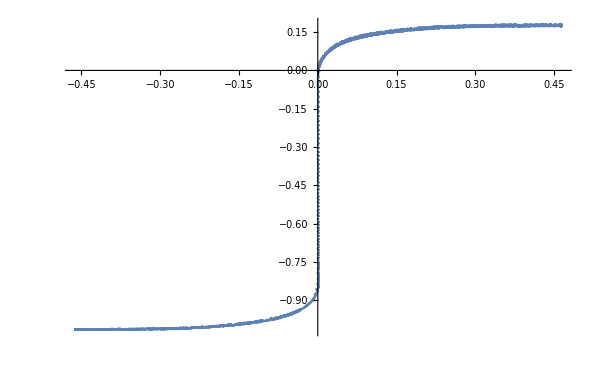

```mathematica
ListPlot[data[[All,{2,3}]]]
```

## Parameters

```mathematica
da=260*10^(-3);
di=220*10^(-3);
h=30*10^(-3);
```

```mathematica
N1=605;
d=(da+di)/2;
R=0.2;
```

```mathematica
N2=80;
A=h (da-di)/2;
messbereich=100;
fullfaktor=0.9;
```

```mathematica
dataProcessed={N1 #[[1]]/(π d R),(messbereich/1000)((#1⟦2⟧)/(N2 fullfaktor A))}&/@data[[All,{2,3}]];
```

```mathematica
xpos = (Max[dataProcessed[[All,1]]]+Min[dataProcessed[[All,1]]])/2
ypos = (Max[dataProcessed[[All,2]]]+Min[dataProcessed[[All,2]]])/2
```

4.01203

-0.966435

```mathematica
dataShifted={#[[1]]-xpos,#[[2]]-ypos}&/@dataProcessed;
```

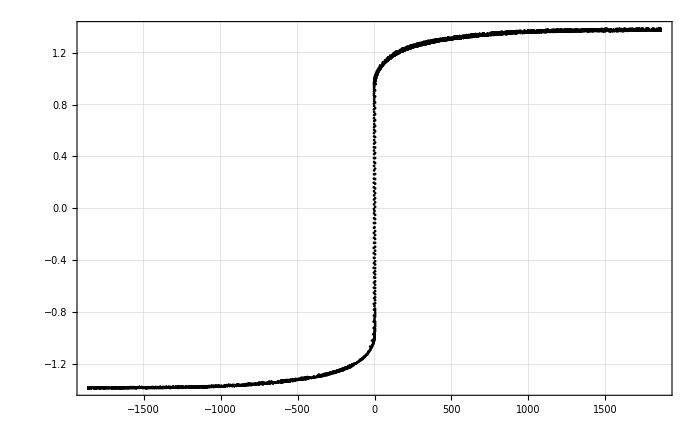

```mathematica
ListPlot[dataShifted,pltsettings,PlotStyle->Black]
```

## Lineare Anpassung

```mathematica
maxData=SortBy[dataShifted,First]
```

```mathematica
fit1data=maxData[[1;;800]];
fit1data[[-1]]
```

{-1336.01,-1.37616}

```mathematica
pars1=ungewichteterReg[fit1data[[All,1]],fit1data[[All,2]]]
```

{-1.36875,7.10689×10^-6,0.000556282,3.35738×10^-7}

```mathematica
fit2data=maxData[[-750;;-1]];
fit2data[[1]]
```

{1428.28,1.37847}

```mathematica
pars2=ungewichteterReg[fit2data[[All,1]],fit2data[[All,2]]]
```

{1.36821,3.2265×10^-6,0.00234001,1.3858×10^-6}

```mathematica
(pars2[[1]]/pars2[[3]]^2 - pars1[[1]]/pars1[[3]]^2)/(1/pars2[[3]]^2 + 1/pars1[[3]]^2)
```

1.36873

```mathematica
1/Sqrt[(1/pars2[[3]]^2 + 1/pars1[[3]]^2)]
```

0.000541199

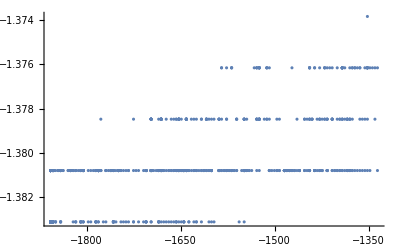

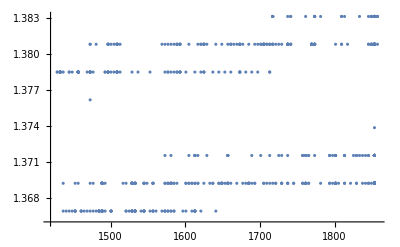

```mathematica
ListPlot[fit1data]
ListPlot[fit2data]
```

## Plots

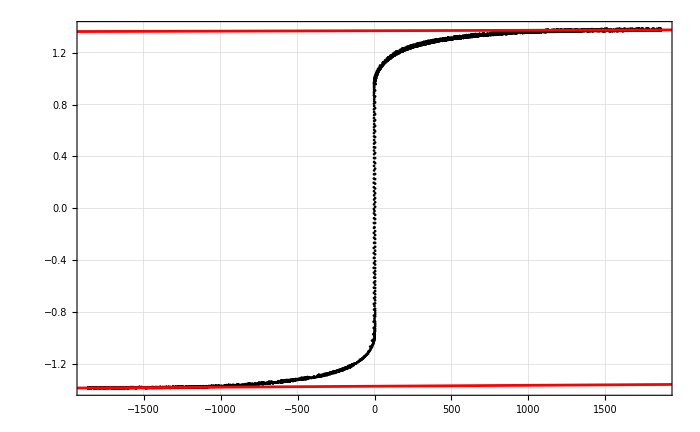

```mathematica
Show[ListPlot[dataShifted,pltsettings,PlotStyle->Black],Plot[{pars1[[1]]+pars1[[2]]x, pars2[[1]]+pars2[[2]]x},{x,-3000,3000},PlotStyle->Red]]
```

```mathematica
Export[NotebookDirectory[]<>"abbildungen/fe-ni sattigungsinduktion raw.pdf",Show[ListPlot[dataShifted,pltsettings,PlotStyle->Black],Plot[{pars1[[1]]+pars1[[2]]x, pars2[[1]]+pars2[[2]]x},{x,-3000,3000},PlotStyle->Red]],Background->None];
```